# Potential SM

```mathematica
ClearAll["Global`*"];
```

```mathematica
V[ϕ_]:=-μh/2 ϕ^2+λ/4 ϕ^4.1c;Clear[μh];
μh=μh/.Solve[(D[V[ϕ],ϕ]==0)/.{ϕ->v},μh][[1]];
Clear[λ];
λ=λ/.(Solve[(D[V[ϕ],{ϕ,2}]/.{ϕ->v})==mh^2,λ])[[1]];
```

```mathematica
D[V[ϕ],{ϕ,2}]
```

-mh^2/2+(3 mh^2 ϕ^2)/(2 v^2)

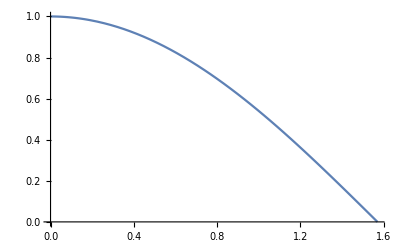

```mathematica
Plot[Cos[x],{x,0,π/2}]
```

# Yukawas

```mathematica
YukawaMatrix={{u1 ϵ^(nQ1+nu1),u2 ϵ^(nQ1+nu2),u3 ϵ^(nQ1+nu3)},{u4 ϵ^(nQ2+nu1),u5 ϵ^(nQ2+nu2),u6 ϵ^(nQ2+nu3)},
{u7 ϵ^(nQ3+nu1),u8 ϵ^(nQ3+nu2),u9 ϵ^(nQ3+nu3)}};
YYdagger=YukawaMatrix.Transpose[YukawaMatrix];MatrixForm[YukawaMatrix]
MatrixForm[YYdagger]
```

(u1 ϵ^(nQ1+nu1) | u2 ϵ^(nQ1+nu2) | u3 ϵ^(nQ1+nu3)
u4 ϵ^(nQ2+nu1) | u5 ϵ^(nQ2+nu2) | u6 ϵ^(nQ2+nu3)
u7 ϵ^(nQ3+nu1) | u8 ϵ^(nQ3+nu2) | u9 ϵ^(nQ3+nu3))

(u1^2 ϵ^(2 nQ1+2 nu1)+u2^2 ϵ^(2 nQ1+2 nu2)+u3^2 ϵ^(2 nQ1+2 nu3) | u1 u4 ϵ^(nQ1+nQ2+2 nu1)+u2 u5 ϵ^(nQ1+nQ2+2 nu2)+u3 u6 ϵ^(nQ1+nQ2+2 nu3) | u1 u7 ϵ^(nQ1+nQ3+2 nu1)+u2 u8 ϵ^(nQ1+nQ3+2 nu2)+u3 u9 ϵ^(nQ1+nQ3+2 nu3)
u1 u4 ϵ^(nQ1+nQ2+2 nu1)+u2 u5 ϵ^(nQ1+nQ2+2 nu2)+u3 u6 ϵ^(nQ1+nQ2+2 nu3) | u4^2 ϵ^(2 nQ2+2 nu1)+u5^2 ϵ^(2 nQ2+2 nu2)+u6^2 ϵ^(2 nQ2+2 nu3) | u4 u7 ϵ^(nQ2+nQ3+2 nu1)+u5 u8 ϵ^(nQ2+nQ3+2 nu2)+u6 u9 ϵ^(nQ2+nQ3+2 nu3)
u1 u7 ϵ^(nQ1+nQ3+2 nu1)+u2 u8 ϵ^(nQ1+nQ3+2 nu2)+u3 u9 ϵ^(nQ1+nQ3+2 nu3) | u4 u7 ϵ^(nQ2+nQ3+2 nu1)+u5 u8 ϵ^(nQ2+nQ3+2 nu2)+u6 u9 ϵ^(nQ2+nQ3+2 nu3) | u7^2 ϵ^(2 nQ3+2 nu1)+u8^2 ϵ^(2 nQ3+2 nu2)+u9^2 ϵ^(2 nQ3+2 nu3))

```mathematica
Eigenvalues[YYdagger]
```

{Root[-u3^2 u5^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u5 u6 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u6^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u3^2 u4 u5 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u5 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u6^2 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u3^2 u4^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u4 u6 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u6^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u5 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u5^2 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2^2 u4 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u5 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u4^2 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u4 u5 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u4 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1^2 u5 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u4^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u4 u5 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u5^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+(u2^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)-2 u1 u2 u4 u5 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u1^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u2^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)-2 u1 u2 u7 u8 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u1^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u5^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)-2 u4 u5 u7 u8 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u4^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u3^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)-2 u1 u3 u4 u6 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u1^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u3^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)-2 u1 u3 u7 u9 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u1^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u6^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)-2 u4 u6 u7 u9 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u4^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u3^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)-2 u2 u3 u5 u6 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u2^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u3^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)-2 u2 u3 u8 u9 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u2^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u6^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)-2 u5 u6 u8 u9 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)+u5^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)) #1+(-u1^2 ϵ^(2 nQ1+2 nu1)-u4^2 ϵ^(2 nQ2+2 nu1)-u7^2 ϵ^(2 nQ3+2 nu1)-u2^2 ϵ^(2 nQ1+2 nu2)-u5^2 ϵ^(2 nQ2+2 nu2)-u8^2 ϵ^(2 nQ3+2 nu2)-u3^2 ϵ^(2 nQ1+2 nu3)-u6^2 ϵ^(2 nQ2+2 nu3)-u9^2 ϵ^(2 nQ3+2 nu3)) #1^2+#1^3&,1],Root[-u3^2 u5^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u5 u6 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u6^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u3^2 u4 u5 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u5 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u6^2 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u3^2 u4^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u4 u6 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u6^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u5 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u5^2 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2^2 u4 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u5 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u4^2 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u4 u5 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u4 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1^2 u5 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u4^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u4 u5 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u5^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+(u2^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)-2 u1 u2 u4 u5 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u1^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u2^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)-2 u1 u2 u7 u8 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u1^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u5^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)-2 u4 u5 u7 u8 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u4^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u3^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)-2 u1 u3 u4 u6 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u1^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u3^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)-2 u1 u3 u7 u9 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u1^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u6^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)-2 u4 u6 u7 u9 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u4^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u3^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)-2 u2 u3 u5 u6 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u2^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u3^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)-2 u2 u3 u8 u9 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u2^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u6^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)-2 u5 u6 u8 u9 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)+u5^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)) #1+(-u1^2 ϵ^(2 nQ1+2 nu1)-u4^2 ϵ^(2 nQ2+2 nu1)-u7^2 ϵ^(2 nQ3+2 nu1)-u2^2 ϵ^(2 nQ1+2 nu2)-u5^2 ϵ^(2 nQ2+2 nu2)-u8^2 ϵ^(2 nQ3+2 nu2)-u3^2 ϵ^(2 nQ1+2 nu3)-u6^2 ϵ^(2 nQ2+2 nu3)-u9^2 ϵ^(2 nQ3+2 nu3)) #1^2+#1^3&,2],Root[-u3^2 u5^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u5 u6 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u6^2 u7^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u3^2 u4 u5 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u5 u6 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u6^2 u7 u8 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u3^2 u4^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u4 u6 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u6^2 u8^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u2 u3 u4 u5 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u3 u5^2 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2^2 u4 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u5 u6 u7 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u2 u3 u4^2 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u3 u4 u5 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-2 u1 u2 u4 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1^2 u5 u6 u8 u9 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u2^2 u4^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+2 u1 u2 u4 u5 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)-u1^2 u5^2 u9^2 ϵ^(2 nQ1+2 nQ2+2 nQ3+2 nu1+2 nu2+2 nu3)+(u2^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)-2 u1 u2 u4 u5 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u1^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu2)+u2^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)-2 u1 u2 u7 u8 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u1^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu2)+u5^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)-2 u4 u5 u7 u8 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u4^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu2)+u3^2 u4^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)-2 u1 u3 u4 u6 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u1^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu1+2 nu3)+u3^2 u7^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)-2 u1 u3 u7 u9 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u1^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu1+2 nu3)+u6^2 u7^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)-2 u4 u6 u7 u9 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u4^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu1+2 nu3)+u3^2 u5^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)-2 u2 u3 u5 u6 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u2^2 u6^2 ϵ^(2 nQ1+2 nQ2+2 nu2+2 nu3)+u3^2 u8^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)-2 u2 u3 u8 u9 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u2^2 u9^2 ϵ^(2 nQ1+2 nQ3+2 nu2+2 nu3)+u6^2 u8^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)-2 u5 u6 u8 u9 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)+u5^2 u9^2 ϵ^(2 nQ2+2 nQ3+2 nu2+2 nu3)) #1+(-u1^2 ϵ^(2 nQ1+2 nu1)-u4^2 ϵ^(2 nQ2+2 nu1)-u7^2 ϵ^(2 nQ3+2 nu1)-u2^2 ϵ^(2 nQ1+2 nu2)-u5^2 ϵ^(2 nQ2+2 nu2)-u8^2 ϵ^(2 nQ3+2 nu2)-u3^2 ϵ^(2 nQ1+2 nu3)-u6^2 ϵ^(2 nQ2+2 nu3)-u9^2 ϵ^(2 nQ3+2 nu3)) #1^2+#1^3&,3]}

# Potential SM+U(1)flavon

```mathematica
ClearAll["Global`*"];
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};S=U1+I U2;
V0[Gp_,Gm_,G0_,h_,u1_,u2_]:=ComplexExpand[-μh Φc.Φ+μs S*S+λ(Φc.Φ)^2+λs(S*S)^2+λhs S*S Φc.Φ]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,U1->u1/√2,U2->u2/√2};
```

```mathematica
V0[0,0,0,h,s,0]
```

(h^4 λ)/4+1/4 h^2 s^2 λhs+(s^4 λs)/4-(h^2 μh)/2+(s^2 μs)/2

```mathematica
Clear[μh];μh=μh/.Solve[(D[V0[0,0,0,h,s,0],h]/.{h->v,s->f})==0,μh][[1]];
Clear[μs];μs=μs/.Solve[(D[V0[0,0,0,h,s,0],s]/.{h->v,s->f})==0,μs][[1]];
```

```mathematica
μh
```

1/2 (2 v^2 λ+f^2 λhs)

```mathematica
μs
```

1/2 (-v^2 λhs-2 f^2 λs)

```mathematica
massmat[i_,j_]:=D[V0[0,0,0,h,s,0],{h,s}[[i]],{h,s}[[j]]]
```

```mathematica
massmatVacuum=Table[massmat[i,j],{i,1,2},{j,1,2}]/.{h->v,s->f};
```

```mathematica
MatrixForm[Table[massmat[i,j],{i,1,2},{j,1,2}]]
```

(3 h^2 λ-v^2 λ-(f^2 λhs)/2+(s^2 λhs)/2 | h s λhs
h s λhs | (h^2 λhs)/2-(v^2 λhs)/2-f^2 λs+3 s^2 λs)

```mathematica
MatrixForm[massmatVacuum]
```

(2 v^2 λ | f v λhs
f v λhs | 2 f^2 λs)

```mathematica
Rotmatrix={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};
```

```mathematica
RMRT=FullSimplify[Transpose[Rotmatrix].massmatVacuum.Rotmatrix];MatrixForm[RMRT]
```

(2 (v^2 λ Cos[α]^2+f v λhs Cos[α] Sin[α]+f^2 λs Sin[α]^2) | f v λhs Cos[2 α]+(-v^2 λ+f^2 λs) Sin[2 α]
f v λhs Cos[2 α]+(-v^2 λ+f^2 λs) Sin[2 α] | 2 (f^2 λs Cos[α]^2-f v λhs Cos[α] Sin[α]+v^2 λ Sin[α]^2))

```mathematica
Clear[λhs];λhs=λhs/.Solve[RMRT[[1,2]]==0,λhs][[1]];
```

```mathematica
Clear[λ,λs];{λ,λs}={λ,λs}/.Solve[{RMRT[[1,1]]+RMRT[[2,2]]==mh^2+ms^2,RMRT[[1,1]]-RMRT[[2,2]]==mh^2-ms^2},{λ,λs}][[1]];
```

```mathematica
Simplify[TrigFactor[λ]]
```

(mh^2 Cos[α]^2+ms^2 Sin[α]^2)/(2 v^2)

```mathematica
FullSimplify[TrigFactor[λs]]
```

(ms^2 Cos[α]^2+mh^2 Sin[α]^2)/(2 f^2)

```mathematica
FullSimplify[TrigFactor[λhs]]
```

((mh-ms) (mh+ms) Cos[α] Sin[α])/(f v)

```mathematica
Simplify[μs]
```

(Cos[2 α] (-f (mh^2+ms^2) Sec[2 α]+(mh^2-ms^2) (f-v Tan[2 α])))/(4 f)

# Lagrange Interpolation

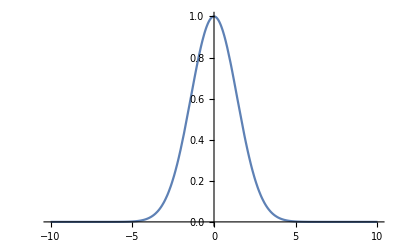

```mathematica
f[x_]:=Exp[-x^2/4];rangeplot={x,-10,10};funplot=Plot[f[x],rangeplot]
```

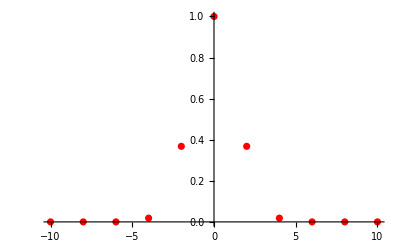

```mathematica
Numdatapoints=5;rangeplot2=Join[rangeplot,{rangeplot[[-1]]/Numdatapoints}];
data=Table[{x,f[x]},Evaluate[rangeplot2]];dataplot=ListPlot[data,PlotStyle->Red]
```

```mathematica
xvals=Transpose[data][[1]];yvals=Transpose[data][[2]];finter[x_]:=Evaluate[Sum[yvals[[j]]Product[If[j!=m,(x-xvals[[m]])/(xvals[[j]]-xvals[[m]]),1],{m,1,Length[data]}],{j,1,Length[data]}]]
```

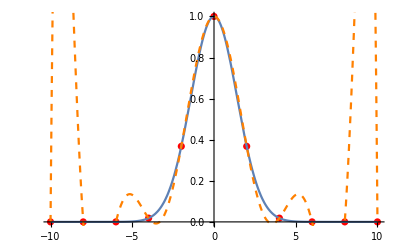

```mathematica
Show[dataplot,funplot,Plot[finter[x],rangeplot,PlotStyle->{Dashed,Orange}]]
```

```mathematica
Clear[ϕbasis];ϕbasis[j_]:=Product[If[j!=m,(x-xvals[[m]])/(xvals[[j]]-xvals[[m]]),1],{m,1,Length[data]}]
```

```mathematica
ϕbasis[2]
```

-((-6-x) (-4-x) (-2-x) (2-x) (4-x) (6-x) (8-x) (10-x) x (10+x))/371589120

```mathematica
Integrate[ϕbasis[2],{x,0,1}]
```

116654149/61312204800